```mathematica
FSize1=30;
FSize2=24;
FontUse="Times";
```

```mathematica
SetDirectory[NotebookDirectory[]<>"..\\"<>"output"];
rvout = Import["rvout.dat","Table"];
(*rvtest1= Table[{rvout[[i,1]]*100,rvout[[i,2]]},{i,1,Length[rvout]}];*)
```

```mathematica
rvtest={{0,0}}
Do[
rvtest=Join[rvtest,{{Abs[rvout[[i,1]]-rvout[[i-1,1]]]*100+rvtest[[-1,1]],rvout[[i,2]]}}]
,{i,2,Length[rvout]}]
rvtest
```

{{0,0}}

{{0,0},{0.2,14.674},{0.4,29.348},{0.6,44.023},{0.8,58.697},{1.,73.371},{1.2,88.045},{1.4,102.72},{1.6,117.39},{1.8,130.65},{2.,139.63},{2.2,146.4},{2.4,151.92},{2.6,156.92},{2.7723,159.95},{2.8859,147.31},{3.0395,134.23},{3.1662,124.16},{3.26,117.06},{3.2943,113.86},{3.311,112.19},{3.3142,111.72},{3.3249,112.4},{3.3375,113.44},{3.3681,115.44},{3.3771,116.21},{3.3909,117.06},{3.3947,116.9},{3.4014,117.18},{3.407,117.4},{3.4139,116.88},{3.4168,116.56},{3.4234,116.72},{3.4238,116.59},{3.4273,116.72},{3.4288,116.73},{3.4423,117.36},{3.4486,117.62},{3.4542,117.82},{3.4596,117.99},{3.4756,118.69},{3.4758,118.57},{3.4892,119.05},{3.497,119.22},{3.503,119.29},{3.505,119.15},{3.5201,119.67},{3.5289,119.87},{3.5426,120.32},{3.5503,120.49},{3.5623,120.88},{3.5708,121.1},{3.5868,121.7},{3.594,121.83},{3.6114,122.48},{3.6208,122.74},{3.6373,123.34},{3.6491,123.67},{3.6614,124.02},{3.675,124.42},{3.6887,124.83},{3.7053,125.36},{3.7193,125.77},{3.7322,126.12},{3.7451,126.48},{3.7621,127.03},{3.7785,127.54},{3.7937,127.98},{3.8097,128.45},{3.8273,128.99},{3.8432,129.45},{3.8594,129.91},{3.876,130.39},{3.8934,130.87},{3.912,131.4},{3.9312,131.95},{3.9506,132.5},{3.971,133.08},{3.9905,133.61},{4.0102,134.15},{4.0293,134.66},{4.052,135.32},{4.0739,135.95},{4.0975,136.63},{4.12,137.24},{4.1432,137.87},{4.167,138.52},{4.192,139.21},{4.2196,139.99},{4.246,140.71},{4.2721,141.39}}

```mathematica
SetDirectory[NotebookDirectory[]<>"..\\"<>"input\\experiment"];
exp= Import["exp_grain_size_1_6mkm.txt","Table"];
exp2= Import["exp_grain_size_40mkm.txt","Table"];
```

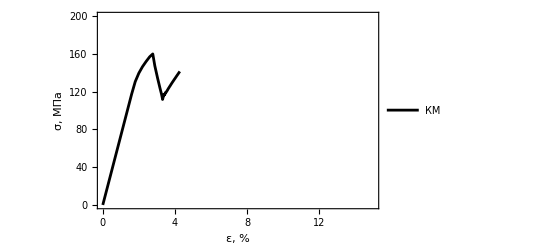

```mathematica
Img=ListLinePlot[{rvtest} ,PlotRange-> {{0,15},{0,200}},Axes->True,Frame->True,FrameLabel->{Style["ε, %",FSize1, FontFamily->"Times"],Style["σ, МПа",FSize1, FontFamily->"Times"]},PlotLegends->Placed[{"КМ","Эксп. 1.6мкм","Эксп. 40мкм"},Above], PlotStyle->{{Black,Thick},{Green,Thick},{Blue,Thick}}, LabelStyle->{FSize1, FontFamily->"Times"},AxesStyle->Directive[FSize2, FontFamily->"Times"],ImageSize->Scaled[.5]]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"..\\"<>"output"];
rvout = Import["grsize.dat","Table"]
```

{{0.00040155,300.,0},{0.00040155,300.,0.2},{0.00040155,300.,0.4},{0.00040155,300.,0.6},{0.00040155,300.,0.8},{0.00040155,300.,1},{0.00040155,300.,1.2},{0.00040155,300.,1.4},{0.00040155,300.,1.6},{0.00040155,300.,1.8},{0.00040155,300.,2},{0.00040155,300.,2.2},{0.00040155,300.,2.4},{0.00040155,300.,2.6},{0.00039765,303.,2.8},{0.00035517,340.,3},{0.00031051,390.,3.2},{0.00027235,446.,3.4},{0.00024082,506.,3.6},{0.00021783,561.,3.8},{0.00019831,618.,4},{0.00018157,677.,4.2},{0.00016728,737.,4.4},{0.00015439,801.,4.6},{0.00014373,863.,4.8},{0.00013271,938.,5},{0.00012286,1017.,5.2},{0.00011296,1111.,5.4},{0.00010435,1208.,5.6},{0.000096392,1314.,5.8},{0.000088626,1437.,6},{0.000081643,1569.,6.2},{0.000075534,1706.,6.4},{0.000069737,1860.,6.6},{0.000064501,2025.,6.8},{0.000059654,2206.,7},{0.000055476,2390.,7.2},{0.00005148,2597.,7.4},{0.000047797,2822.,7.6},{0.000044412,3066.,7.8},{0.000041467,3315.,8},{0.000038529,3607.,8.2},{0.000036003,3902.,8.4},{0.000033606,4230.,8.6},{0.000031376,4588.,8.8},{0.000029285,4983.,9},{0.000027485,5381.,9.2},{0.000025768,5824.,9.4},{0.000024222,6289.,9.6},{0.000022748,6806.,9.8},{0.000021418,7350.,10},{0.000020166,7946.,10.2},{0.000019055,8561.,10.4},{0.000017977,9253.,10.6},{0.000017033,9956.,10.8},{0.00001612,10742.,11},{0.000015305,11553.,11.2},{0.000014529,12444.,11.4},{0.000013812,13396.,11.6},{0.000013149,14409.,11.8},{0.000012534,15491.,12},{0.00001197,16630.,12.2},{0.000011437,17863.,12.4},{0.000010938,19188.,12.6},{0.000010473,20603.,12.8},{0.000010049,22079.,13},{9.6509×10^-6,23657.,13.2},{9.2761×10^-6,25350.,13.4},{8.927×10^-6,27144.,13.6},{8.6027×10^-6,29036.,13.8},{8.2956×10^-6,31067.,14},{8.0079×10^-6,33223.,14.2},{7.7382×10^-6,35508.,14.4},{7.4855×10^-6,37924.,14.6},{7.2491×10^-6,40470.,14.8},{7.027×10^-6,43159.,15},{6.8174×10^-6,46004.,15.2},{6.6204×10^-6,48998.,15.4},{6.433×10^-6,52180.,15.6},{6.2557×10^-6,55540.,15.8},{6.0869×10^-6,59104.,16},{5.9298×10^-6,62791.,16.2},{5.7797×10^-6,66694.,16.4},{5.6381×10^-6,70769.,16.6},{5.5022×10^-6,75084.,16.8},{5.373×10^-6,79610.,17},{5.2499×10^-6,84351.,17.2},{5.1328×10^-6,89301.,17.4},{5.0222×10^-6,94415.,17.6},{4.9152×10^-6,99814.,17.8}}